# Diode

## Funktionen

### Includes

```mathematica
Needs["ErrorBarPlots`"]
```

### Fehlerfunktion(Größtfehler) ∑(|df/dx_i|Δx_i)

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c]);
```

### Gaussfunktion

```mathematica
Gauss[a_]:={Mean[a],StandardDeviation[a]/(√Length[a])}
```

### Basics

```mathematica
fAdd[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a+b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

```mathematica
Fdiv[a1_,da1_,b1_,db1_]:= Module[{f,fe,a,b,da,db},
f=a/b;
fe = GError[f,{a,b},{da,db}];
{f,fe}/.{a->a1,da->da1,b-> b1,db->db1}]
```

```mathematica
Fmult[γ_,dγ_,δ_,dδ_]:= Module[{f,fe,a,b,da,db},
f=a*b;
fe = GError[f,{a,b},{da,db}];
{f,fe}/.{a->γ,da->dγ,b-> δ,db->dδ}]
```

```mathematica
Ff[a1_,da1_,b1_,db1_,c1_,dc1_]:= Module[{f,fe,a,b,c,da,db,dc},
f=a*b/c;
fe = GError[f,{a,b,c},{da,db,dc}];
{f,fe}/.{a->a1,da->da1,b-> b1,db->db1,c->c1,dc->dc1}]
```

## 2.2.) Kalibrierung des Kompensators

```mathematica
dt={{□, □}, {□, □}, {□, □}, {□, □}, {□, □}, {□, □}, {□, □}, {□, □}, {□, □}, {□, □}};
```

```mathematica
ddt = Table[{dt[[x,1]]*0.01+0.001,dt[[x,2]]*0.015+0.01},{x,1,Length[dt]-2}];
```

```mathematica
p1 = Table[{{dt[[x,1]],dt[[x,2]]},ErrorBar[ddt[[x,1]],ddt[[x,2]]]},{x,1,Length[dt]}]
```

({0,-0.01} | ErrorBar(0.001,0.00985)
{0.49,-0.01} | ErrorBar(0.0059,0.00985)
{0.1,-0.01} | ErrorBar(0.002,0.00985)
{0.149,-0.02} | ErrorBar(0.00249,0.0097)
{0.195,-0.01} | ErrorBar(0.00295,0.00985)
{0.246,-0.01} | ErrorBar(0.00346,0.00985)
{0.306,-0.01} | ErrorBar(0.00406,0.00985)
{0.344,-0.01} | ErrorBar(0.00444,0.00985)
{0.393,0} | ErrorBar(0.00493,0.01)
{0.445,0.05} | ErrorBar(0.00545,0.01075)
{0.498,0.26} | ErrorBar(0.00598,0.0139)
{0.548,0.92} | ErrorBar(0.00648,0.0238)
{0.6,3.29} | ErrorBar(0.007,0.05935)
{0.648,9.87} | ErrorBar(0.00748,0.15805)
{0.684,24.07} | ErrorBar(0.00784,0.37105)
{0.701,37.16} | ErrorBar(0.00801,0.5674)
{0.725,70.5} | ErrorBar(0.00825,1.1575)
{0.749,133.1} | ErrorBar(0.00849,2.0965))

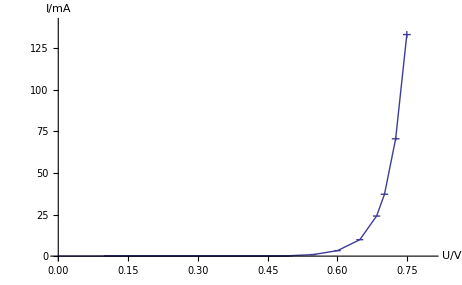

```mathematica
ErrorListPlot[p1,Joined-> True,AxesOrigin-> {0,0},AxesLabel-> {"U/V","I/mA"},PlotRange->{{0,0.8},{0,140}}]
```

```mathematica
pf1=LinearModelFit[dt,x,x]
```

## 2.4)

```mathematica
k4 =0;
```

## 2.5)

## 2.6)